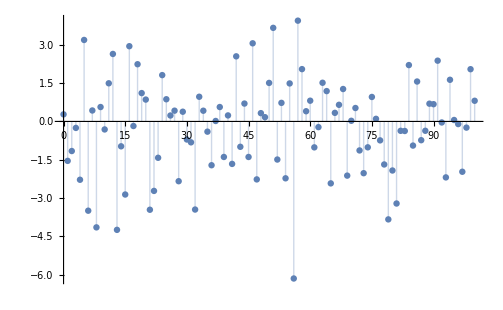

```mathematica
Clear["Global`*"]
(* GARCH process example *)
(* A GarchProcess G(p,q) has: (σ(t))^2=κ+Subscript[α, 1] (x(t-1))^2+⋯+Subscript[α, q] (x(t-q))^2+Subscript[β, 1] (σ(t-1))^2+⋯+Subscript[β, p] (σ(t-p))^2 *)

proc=RandomFunction[GARCHProcess[2,{.1},{.2}],{0,100}];
ListPlot[proc,Filling->Axis]
```

```mathematica
Mean[proc]
```

-0.2282

```mathematica
Variance[proc]
```

3.46556

```mathematica
Mean[GARCHProcess[2,{.1},{.2}][t]]
```

0

```mathematica
Variance[GARCHProcess[2,{.1},{.2}][t]]
```

2.85714

```mathematica
sample1=RandomVariate[GARCHProcess[2,{.1},{.2}][10],10^5];
HH=DistributionFitTest[sample1,Automatic,"HypothesisTestData"]
```

HypothesisTestData[…]

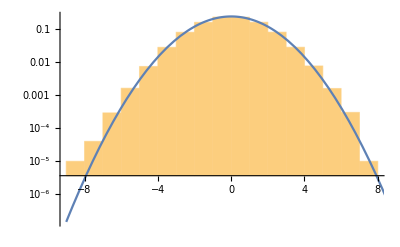

```mathematica
Show[Histogram[sample1,Automatic,"LogPDF"], LogPlot[PDF[HH["FittedDistribution"],x],{x,-9,9}]]
```

```mathematica
DistributionFitTest[sample1]
```

0.218565

```mathematica
KolmogorovSmirnovTest[sample1]
```

0.370955

```mathematica
sample2=RandomVariate[GARCHProcess[2,{.1,.1,.1},{.2,.2,.2}][1000],10^5];
HH1=DistributionFitTest[sample2,Automatic,"HypothesisTestData"]
```

HypothesisTestData[…]

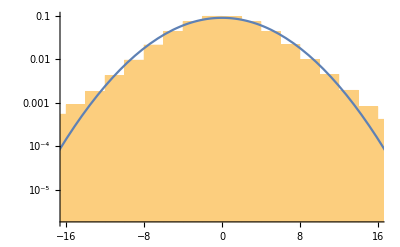

```mathematica
Show[Histogram[sample2,Automatic,"LogPDF"], LogPlot[PDF[HH1["FittedDistribution"],x],{x,-19,19}]]
```